```mathematica
Limit[Sum[(a^k-1)/k,{k,1,Log[a,100]}],{a->1}]
```

{Limit[-HarmonicNumber[Log[100]/Log[a]]-100 a LerchPhi[a,1,1+Log[100]/Log[a]]-Log[1-a],a→1]}

```mathematica
{Limit[-HarmonicNumber[Log[100]/Log[a]]-Log[1-a],a->1]}
```

{-EulerGamma-ⅈ π-Log[Log[100]]}

```mathematica
Limit[Sum[(a^k)/k,{k,1,Log[a,100]}],{a->1}]
```

{Limit[-100 a LerchPhi[a,1,1+Log[100]/Log[a]]-Log[1-a],a→1]}

```mathematica
Limit[Sum[(a^k+1)/k,{k,1,Log[a,100]}],{a->1}]
```

{Limit[HarmonicNumber[Log[100]/Log[a]]-100 a LerchPhi[a,1,1+Log[100]/Log[a]]-Log[1-a],a→1]}

```mathematica
{Limit[-HarmonicNumber[100/Log[a]]-Log[1-a],a->1]}
```

{-EulerGamma-ⅈ π-Log[100]}

```mathematica
{Limit[HarmonicNumber[Log[100]/Log[a]]+Log[1-a],a->1]}
```

{EulerGamma+ⅈ π+Log[Log[100]]}

```mathematica
Log[0]
```

-∞

```mathematica
N[Integrate[ 1/x,{x,1,1/2}]]
```

-0.693147

```mathematica
-Log[1-2]
```

-ⅈ π

```mathematica
-Log[1-3/4]
```

Log[4]

```mathematica
fc[a_]:=-HarmonicNumber[Log[100]/Log[a]]-Log[1-a]
```

```mathematica
N[fc[1-1/1000000]]
```

6.08307

ConditionalExpression[Gamma[s] PolyLog[s,1],Re[s]>1]

```mathematica
ts[n_, s_]:=Integrate[ x^(s-1)/(E^x-1),{x,0,-Log[n]}]/Gamma[s]
```

```mathematica
N[ts[100,0]]
```

```mathematica
{Limit[PolyGamma[Log[100]/Log[a]]+Log[1-a],a->1]}
```

{ⅈ π+Log[Log[100]]}

```mathematica
Limit[Sum[(a^k)/k,{k,1,Log[a,100]}],{a->1}]
```

{Limit[-100 a LerchPhi[a,1,1+Log[100]/Log[a]]-Log[1-a],a→1]}

```mathematica
Limit[Sum[ (a^k)/k,{k,1,Log[a,100]}],{a->1}]
```

{Limit[-100 a LerchPhi[a,1,1+Log[100]/Log[a]]-Log[1-a],a→1]}

```mathematica
Limit[Sum[ (a^k)/k,{k,Log[a,100],Infinity}],{a->7}]
```

{100 HurwitzLerchPhi[7,1,Log[100]/Log[7]]}

```mathematica
Limit[Sum[ (a^k)/k,{k,1,Log[a,100]}],{a->7}]
```

{-ⅈ π-700 LerchPhi[7,1,Log[700]/Log[7]]-Log[6]}

```mathematica
Limit[Sum[ (a^k)/k,{k,1,Infinity}],{a->b}]
```

{-Log[1-b]}

```mathematica
Log[1-(101/100)]
```

ⅈ π-Log[100]

```mathematica
Log[-99]
```

ⅈ π+Log[99]

```mathematica
E^(Pi I +Log[99])
```

-99

```mathematica
Limit[Sum[(a^k)/k,{k,Log[a,100],Infinity}],{a->1}]
```

{Limit[100 HurwitzLerchPhi[a,1,Log[100]/Log[a]],a→1]}

```mathematica
vv[n_,a_]:=Sum[(a^k)/k,{k,Log[a,n],Infinity}]
```

```mathematica
vv[100,1.1]
```

Sum::div: Sum does not converge.

∑_(k=48.3177)^∞ 1.1^k/k

Integrate::idiv: Integral of Log[t]^-1 + a does not converge on {1, ∞}.

```mathematica
Integrate[Log[t^-1]^(a-1),{t,0,1}]
```

ConditionalExpression[Gamma[a],Re[a]>0]

```mathematica
Integrate[Log[t^-1]^(z-1),{t,0,1/2}]
```

Gamma[z,Log[2]]

```mathematica
Integrate[Log[t^-1]^(z-1),{t,0,1/3}]
```

Gamma[z,Log[3]]

```mathematica
Integrate[Log[t^-1]^(a-1),{t,1/(n^(1-s)),1}]
```

ConditionalExpression[Gamma[a]-Gamma[a,-Log[n^(-1+s)]],Re[a]>0]

```mathematica
Integrate[Log[t^-1]^(z-1),{t,1/3,1}]
```

ConditionalExpression[Gamma[z]-Gamma[z,Log[3]],Re[z]>0]

```mathematica
N[Gamma[z]-Gamma[z,Log[3]]/.z->2]
```

0.300463

```mathematica
N[Gamma[z,0,Log[3]]/.z->2]
```

0.300463

```mathematica
Gamma[a]-Gamma[a,-Log[n^(-1+s)]]/.{a->2,n->100,s->2}
```

1-Gamma[2,-Log[100]]

```mathematica
Integrate[ t^(s-1) E^-t,{t,0,Infinity}]
```

ConditionalExpression[Gamma[s],Re[s]>0]

```mathematica
Integrate[ t^(s-1) E^(-n t),{t,0,Infinity}]
```

ConditionalExpression[n^-s Gamma[s],Re[s]>0&&Re[n]>0]

```mathematica
Integrate[ t^(s-1) E^(-n t),{t,0,x}]
```

ConditionalExpression[x^s (n x)^-s (Gamma[s]-Gamma[s,n x]),Re[s]>0]

```mathematica
Integrate[ Sum[t^(s-1) E^(-n t),{n,1,Infinity}],{t,0,Infinity}]
```

ConditionalExpression[Gamma[s] PolyLog[s,1],Re[s]>1]

```mathematica
Integrate[ Sum[t^(s-1) E^(-n t),{n,1,Infinity}],{t,0,x}]
```

∫_0^x t^(-1+s)/(-1+ⅇ^t)ⅆt

```mathematica
Integrate[ Sum[t^(s-1) E^(-n t),{n,1,x}],{t,0,x}]
```

∫_0^x (ⅇ^(-t x) (-1+ⅇ^(t x)) t^(-1+s))/(-1+ⅇ^t)ⅆt

```mathematica
Expand[(ⅇ^(-t x) (-1+ⅇ^(t x)) t^(-1+s))/(-1+ⅇ^t)]
```

```mathematica
FullSimplify[t^(-1+s)/(-1+ⅇ^t)-(ⅇ^(-t x) t^(-1+s))/(-1+ⅇ^t)]
```

```mathematica
Integrate[t^(-1+s)/(-1+ⅇ^t)-(ⅇ^(-t x) t^(-1+s))/(-1+ⅇ^t),{t,0,x}]
```

∫_0^x (t^(-1+s)/(-1+ⅇ^t)-(ⅇ^(-t x) t^(-1+s))/(-1+ⅇ^t))ⅆt

```mathematica
Integrate[t^(-1+s)/(-1+ⅇ^t),{t,0,x}]
```

∫_0^x t^(-1+s)/(-1+ⅇ^t)ⅆt

```mathematica
Integrate[-(ⅇ^(-t x) t^(-1+s))/(-1+ⅇ^t),{t,0,x}]
```

∫_0^x -(ⅇ^(-t x) t^(-1+s))/(-1+ⅇ^t)ⅆt

```mathematica
bb[x_,s_]:=∫_0^x (ⅇ^(-t x) (-1+ⅇ^(t x)) t^(-1+s))/(-1+ⅇ^t)ⅆt
```

Integrate::idiv: Integral of -1./t - ⅇ^t\ t + ⅇ^-1.00018\ t/t - ⅇ^t\ t does not converge on {0, 1.00018}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.63103×10^-29}. NIntegrate obtained 23236. and 19755. for the integral and error estimates.

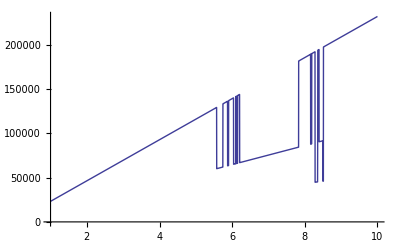

```mathematica
Plot[bb[n,0],{n,1,10}]
```

```mathematica
Integrate[Log[t^-1]^(2),{t,1/(n^(1-p)),1}]
```

ConditionalExpression[2-n^(-1+p) (2+Log[n^(1-p)] (2+Log[n^(1-p)])),(n^p/(-n+n^p)≠0&&Re[1/(-1+n^(1-p))]≥0)||Re[1/(-1+n^(1-p))]≤-1||1/(-1+n^(1-p))∉Reals]

```mathematica
Expand[ConditionalExpression[1-n^(-1+p) (1+Log[n^(1-p)]),(n^p/(-n+n^p)≠0&&Re[1/(-1+n^(1-p))]≥0)||Re[1/(-1+n^(1-p))]≤-1||1/(-1+n^(1-p))∉Reals]]
```

ConditionalExpression[1-n^(-1+p)-n^(-1+p) Log[n^(1-p)],(n^p/(-n+n^p)≠0&&Re[1/(-1+n^(1-p))]≥0)||Re[1/(-1+n^(1-p))]≤-1||1/(-1+n^(1-p))∉Reals]

```mathematica
Integrate[Log[rr^-1]^(1),{rr,1/(m^(1-ss)),1}]
```

$Aborted